# Lab 9: Animation and Collision

## Computer Graphics Lab, Wolfram Mathematica

```mathematica
SetOptions[EvaluationNotebook[],ShowCellLabel->True];
```

```mathematica
SetOptions[{Plot,Plot3D,ContourPlot,ContourPlot3D,DensityPlot,ParametricPlot,ParametricPlot3D,ListPlot,ListLinePlot,ListPointPlot3D,Graphics,Graphics3D,PolarPlot},ImageSize->Small,AxesLabel->{"x","y","z"}];
```

```mathematica
(* Problem 1 *)
```

```mathematica
SP2[t_]:=0.15{(3/4)*(t)*(t^2-11),t^4-12*t^2,(1/30)*(t)*(t^2-1)*(t^2-3)*(t^2-9)*(t^2-12)}
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
D[SP2[t],t]
```

{0.225 t^2+0.1125 (-11+t^2),0.15 (-24 t+4 t^3),0.01 t^2 (-12+t^2) (-9+t^2) (-3+t^2)+0.01 t^2 (-12+t^2) (-9+t^2) (-1+t^2)+0.01 t^2 (-12+t^2) (-3+t^2) (-1+t^2)+0.01 t^2 (-9+t^2) (-3+t^2) (-1+t^2)+0.005 (-12+t^2) (-9+t^2) (-3+t^2) (-1+t^2)}

```mathematica
dSP2[t_]:=Evaluate[D[SP2[t],t]]
```

```mathematica
Traj2=ParametricPlot3D[SP2[t],{t,-3.5,3.5}]
```

-Graphics3D-

```mathematica
SpikeyT2=Import["spikeymodel.stl","PolygonObjects"];
```

```mathematica
GSpiketT2=Graphics3D[SpikeyT2,Axes->True,PlotRange->3,AxesOrigin->{0,0,0}]
```

-Graphics3D-

```mathematica
PositionT2[P_]:=GeometricTransformation[SpikeyT2,TranslationTransform[P]]
MoveSpikeyT2[t_]:=Graphics3D[PositionT2[SP2[t]],Axes->True,PlotRange->9]
```

```mathematica
Table[MoveSpikeyT2[t],{t,0,3}]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
Manipulate[Show[MoveSpikeyT2[t],Traj2,PlotRange->6.5],{t,-3.5,3.5}]
```

```mathematica
(* Problem 1A *)
```

```mathematica
Position1A[P_,a_]:=GeometricTransformation[SpikeyT2,Composition[TranslationTransform[P],RotationTransform[a,{0,0,1}]]]
MoveSpikey1A[t_,a_]:=Graphics3D[Position1A[SP2[t],a],Axes->True,PlotRange->9]
```

```mathematica
Manipulate[Show[MoveSpikey1A[t,a],Traj2,PlotRange->6.5],{t,-3.5,3.5},{a,0,8}]
```

```mathematica
Manipulate[Show[MoveSpikey1A[t,5*t],Traj2,PlotRange->6.5],{t,-3.5,3.5}]
```

```mathematica
SP2[t]
```

{0.1125 t (-11+t^2),0.15 (-12 t^2+t^4),0.005 t (-12+t^2) (-9+t^2) (-3+t^2) (-1+t^2)}

```mathematica
NP=200
```

200

```mathematica
Traj200=Array[SP2,NP,{-3.5,3.5}];
```

```mathematica
PTraj200=Line[Traj200];
```

```mathematica
GTraj200=Graphics3D[{Blue,Thick,{PTraj200}},Axes->True]
```

-Graphics3D-

```mathematica
Position1B[P_,a_]:=GeometricTransformation[SpikeyT2,Composition[TranslationTransform[P],RotationTransform[a,{0,0,1}]]]
MoveSpikey1B[t_,a_]:=Graphics3D[Position1B[Traj200[[t]],a],Axes->True,PlotRange->9]
```

```mathematica
Manipulate[Show[MoveSpikey1B[t,5*t],GTraj200,PlotRange->6.5],{t,1,200,1}]
```

```mathematica
(* Problem 2 *)
```

```mathematica
t2=0;step2=0.1;
```

```mathematica
Menu2=Framed[PopupMenu[Dynamic[menu2],{False->"Stop",True->"Start"},Background->Red]]
```

```mathematica
Manip1A=Manipulate[
If[menu2,step2=0.075,step2=0];
If[t2>=3.5,t2=-3.5];
t2+=step2;
G2=Show[MoveSpikey1A[t2,t2],Traj2];
G2,{t,0,0}]
```

```mathematica
(* Problem 3 *)
```

```mathematica
Rect3={LightBlue,Rectangle[{0,0},{1,1}]}
```

{RGBColor[0.87, 0.94, 1],Rectangle[{0,0},{1,1}]}

```mathematica
{RGBColor[0.87, 0.94, 1],Rectangle[{0,0},{1,1}]}
```

{RGBColor[0.87, 0.94, 1],Rectangle[{0,0},{1,1}]}

```mathematica
R3=0.1;
```

```mathematica
D3[x_,y_]:={Blue,Disk[{x,y},R3]}
```

```mathematica
x3=0.5;y3=0.5;vx3=1;vy3=Pi/2;step3=0.01;
```

```mathematica
O3[x_,y_]:={Rect3,D3[x,y]}
```

```mathematica
Menu3=PopupMenu[Dynamic[menu3],{False->"Stop",True->"Start"},MenuStyle->{Orange,"Input"}]
```

```mathematica
Manipulate[
If[menu3,step3=0.01,step3=0];
x3=x3+vx3*step3;
y3=y3+vy3*step3;
(*If[Abs[x3-1]<=R3||Abs[x3]<=R3,vx3=-vx3];
  If[Abs[y3-1]<=R3||Abs[y3]<=R3,vy3=-vy3];*)
If[(x3+R3)>=1||(x3-R3)<=0,vx3=-vx3];
If[(y3+R3)>=1||(y3-R3)<=0,vy3=-vy3];
G3=Graphics[O3[x3,y3],PlotRange->{{-0.2,1.2},{-0.2,1.2}},Axes->True];
G3,{t,0,0}]
```

```mathematica
Rot3B[O_,x_,y_,a_]:=GeometricTransformation[O[x,y],RotationTransform[a,{1/2,1/2}]]
```

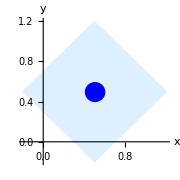

```mathematica
Graphics[Rot3B[O3,1/2,1/2,Pi/4],PlotRange->{{-0.2,1.2},{-0.2,1.2}},Axes->True,AxesOrigin->{0,0}]
```

```mathematica
Rot3B[O_,x_,y_,a_]:=GeometricTransformation[O[x,y],RotationTransform[a,{1/2,1/2}]]
```

```mathematica
MenuR3B=PopupMenu[Dynamic[menur3],{False->"Stop",True->"Start"},MenuStyle->{Purple,"Input"}]
```

```mathematica
x3B=0.5;y3B=0.5;vx3B=1;vy3B=Pi/2;step3B=0.01;R3=0.1;a3B=0;
```

```mathematica
Manipulate[
If[menur3,step3B=0.01,step3B=0];
x3B=x3B+vx3B*step3B;
y3B=y3B+vy3B*step3B;
If[x3B+R3>=1||x3B-R3<=0,vx3B=-vx3B];
If[y3B+R3>=1||y3B-R3<=0,vy3B=-vy3B];
Graphics[Rot3B[O3,x3B,y3B,a],PlotRange->{{-0.2,1.2},{-0.2,1.2}},Axes->True],{a,0,1}]
```

```mathematica
(* Problem 4 *)
```

```mathematica
Norm[{X,Y}]
```

√(Abs[X]^2+Abs[Y]^2)

```mathematica
Init4[]:=Module[{},
x4=0.5;
y4=0.5;
vx4=1;
vy4=Pi/2;
step4=0.1;
a4=0;
RC4=5/2;
RD4=0.25;
ad4=0;
Rad4=7/2;
vxold=0;
vyold=0;
0]
```

```mathematica
Init4[]
```

0

```mathematica
BigCircle4=Circle[{0,0},RC4];
```

```mathematica
D4[x_,y_]:={Blue,Disk[{x,y},RD4]}
```

```mathematica
O4[x_,y_]:={BigCircle4,D4[x,y]}
```

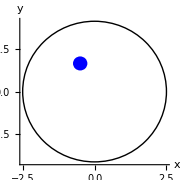

```mathematica
Graphics[O4[-0.5,1],Axes->True]
```

```mathematica
Init4[]
```

0

```mathematica
Menu4=PopupMenu[Dynamic[menu4],{False->"Stop",True->"Start"},MenuStyle->{Brown,"Input"},Background->Yellow]
```

```mathematica
Manip4=Manipulate[
If[menu4,step4=0.05,step4=0];
vxold=vx4;
vyold=vy4;

(* Speed-up if near center *)
If[(Norm[{x4,y4}])^2<=(RC4-2*RD4)^2&&menu4,
{vx4=vx4*RandomReal[{1,2}],vy4=vy4*RandomReal[{1,2}]}];

x4+=vx4*step4;
y4+=vy4*step4;
vx4=vxold;
vy4=vyold;

If[(Norm[{x4,y4}])^2>=(RC4-RD4)^2,{vx4=-vx4;vy4=-vy4}];
GB4=Graphics[O4[x4,y4],PlotRange->5,Axes->True];
GB4,{t,0,0}]
```

```mathematica
Menu5=PopupMenu[Dynamic[menu5],{False->"Stop",True->"Start"},MenuStyle->{Pink,"Input"},Background->Yellow]
```

```mathematica
O42[x_,y_,a4_]:=GeometricTransformation[O4[x,y],Composition[RotationTransform[a4],TranslationTransform[{5/2,0}]]]
```

```mathematica
Manip5=Manipulate[
If[menu5,step4=0.05,step4=0];
vxold=vx4;
vyold=vy4;

(* Speed-up if near center *)
If[(Norm[{x4,y4}])^2<=(RC4-2*RD4)^2&&menu5,
{vx4=vx4*RandomReal[{1,2}],vy4=vy4*RandomReal[{1,2}]}];

x4+=vx4*step4;
y4+=vy4*step4;
vx4=vxold;
vy4=vyold;

If[(Norm[{x4,y4}])^2>=(RC4-RD4)^2,{vx4=-vx4;vy4=-vy4}];
GB4=Graphics[O42[x4,y4,a4],PlotRange->5,Axes->True];
GB4,{a4,0,2Pi}];
```